# Testing the ‘Rosetta Stone’ approach by comparing the Fourier transfer function from the linear response

## Written by Maurizio Mattia, January 2023, Rome - Italy

## Script plotting the panels in Figs. 4-5 of (Vinci & Mattia, 2024)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["LIFLibrary.m",Path-> NotebookDirectory[]]
```

```mathematica
Needs["NumericalCalculus`"]
```

## Neuron parameters used in this notebook

Membrane potential decay time in seconds:

```mathematica
τ=0.020;
```

Emission threshold in mV:

```mathematica
Vt=20.;
```

Reset potential in mV (0 is the resting potential):

```mathematica
Vr=0.;
```

Absolute refractory period in seconds:

```mathematica
Tarp=0.;
```

Note that in what follows both the mean (μ) and standard deviation (σ) of the input current are expressed in mV, meaning that actually they are respectively μ τ and σ √τ.

This is the current-to-rate gain function. To have it in Hz it must be divided by τ.

```mathematica
Φ[Xr_,Xt_]:=1/MFPT[Xr,Xt];
```

### Guesses for the eigenvalues λ_n at μτ=(v_thr + v_res)/2

The theoretical guesses from Eq. (13.9.10) in DLMF 2010. This is valid for large (n^2 π^2)/(2 Xt^2).

```mathematica
LambdasAtBifurcationLargeN[Xt_,NumOfLambdas_]:=
Table[(-3 n^2 π^2+3 Xt^2-Xt^4)/(6 Xt^2),{n,NumOfLambdas}];
```

```mathematica
LambdasBeforeBifurcation[Xr_,Xt_,λτRange_]:=Module[{λτ={},z},λτ=Flatten[Append[λτ,z/.NSolve[CERS[z,Xr,Xt]==0 && Min[λτRange]<z<Max[λτRange],z,Reals]]];
Sort[λτ,Re[#1]>Re[#2]&]
]
```

```mathematica
LambdasAtBifurcation[Xt_,λτRange_]:=Module[{λτ,n},
λτ=2Range[Quotient[Min[λτRange],2],Quotient[Max[λτRange],2]];
λτ=If[λτ[[1]]<Min[λτRange],Take[λτ,1-Length[λτ]],λτ];
For[n=1,Min[λτRange]<(-3 n^2 π^2+3 Xt^2-Xt^4)/(6 Xt^2),n++,AppendTo[λτ,(-3 n^2 π^2+3 Xt^2-Xt^4)/(6 Xt^2)]];
Sort[λτ,Greater]
]
```

```mathematica
LambdasBeyondBifurcation[Xr_,Xt_,λτRange_]:=Module[{λτ,λτ0,z,ExitFor,PhiTau,n},
PhiTau=Φ[Xr,Xt];
ExitFor=False;
λτ={};
For[n=1,Not[ExitFor],n++,
λτ0=-(2 π^2 n^2)/(Xt-Xr)^2+ⅈ 2π PhiTau  n;
If[Re[λτ0]<=Max[λτRange],
If[Re[λτ0]>=Min[λτRange],AppendTo[λτ,λτ0],ExitFor=True],Null]
];
λτ=GetLambdasFromGuess[Xr,Xt,λτ];
λτ=Flatten[Append[λτ,Conjugate[λτ]]];
λτ=Flatten[Append[λτ,z/.NSolve[CERS[z,Xr,Xt]==0 && Min[λτRange]<z<Max[λτRange],z,Reals]]];
Sort[λτ,Re[#1]>Re[#2]&]
]
```

Revised expression of the non-normalized (NN) eigenfunctions ψ(x,λ) referring to (Ricciardi & Sato, 1988) [RS88] and the related characteristic equation for the eigenvalues:

```mathematica
(* This is the same as the following Initialization cell but can be used to define the characteristic equation as in (Mattia & Del Giudice 2002). This is why here the eigenfunctions ψ are multiplied by Gamma[λ/2]. *)ψNN[x_,λ_]=Gamma[λ/2]/Gamma[(λ+1)/2] Hypergeometric1F1[λ/2,1/2,x^2]+2x Hypergeometric1F1[(1+λ)/2,3/2,x^2];
CERS[λ_,Xr_,Xt_]=ψNN[Xt,λ]-ψNN[Xr,λ];
```

```mathematica
ψNN[x_,λ_]=Hypergeometric1F1[λ/2,1/2,x^2]/Gamma[(λ+1)/2]+2x Hypergeometric1F1[(1+λ)/2,3/2,x^2]/Gamma[λ/2];
ρISI[s_,Xr_,Xt_]=ψNN[Xr,s]/ψNN[Xt,s];
CERS[λ_,Xr_,Xt_]=ρISI[λ,Xr,Xt]-1;
```

```mathematica
h[s_,Xr_,Xt_]=ρISI[s,Xr,Xt]/(1-ρISI[s,Xr,Xt]);
```

Partial derivative of the eigenfunction to be used in the Fourier transfer function:

```mathematica
DxψNN[x_,λ_]=Simplify[D[ψNN[x,λ], x]]
```

(2 x λ Hypergeometric1F1[1+λ/2,3/2,x^2])/Gamma[(1+λ)/2]+1/(3 Gamma[λ/2])(6 Hypergeometric1F1[(1+λ)/2,3/2,x^2]+4 x^2 (1+λ) Hypergeometric1F1[(3+λ)/2,5/2,x^2])

Expressions for the eigenfunctions ψ based on parabolic cylinder functions, equivalent to the previous ones but in several (μ,σ)-regimes more numerically stable (to compute for instance the Fourier transfer function at high ω:

```mathematica
ψNND[x_,λ_]=ⅇ^(x^2/2)ParabolicCylinderD[-λ,-√2 x];
ρISID[s_,Xr_,Xt_]=ψNND[Xr,s]/ψNND[Xt,s];
(*CERSD[λ_,Xr_,Xt_]=ρISID[λ,Xr,Xt]-1;*)
CERSD[λ_,Xr_,Xt_]=ψNND[Xr,λ]-ψNND[Xt,λ];
```

```mathematica
DxψNND[x_,λ_]=Simplify[D[ψNND[x,λ], x]]
```

ⅇ^(x^2/2) (√2 ParabolicCylinderD[1-λ,-√2 x]+2 x ParabolicCylinderD[-λ,-√2 x])

### Supra - threshold example network of LIF neurons for the Figures of (Vinci & Mattia, 2024)

Drift-dominated workbench where   μτ>μτ^*=(Vt+Vr)/2.

```mathematica
μτ=Vt-3;
σ2τ=4.5^2;
```

```mathematica
Module[{λτRange={-250,-0.1},n},
XtTest=(Vt-μτ)/(√σ2τ);XrTest=(Vr-μτ)/(√σ2τ);

ντ=Φ[XrTest,XtTest];
Print["Φ[Xr,Xt] = ",ντ];
Print["Φ[Xr,Xt]/τ = ",ντ/τ," Hz"];

λτTest=LambdasBeyondBifurcation[XrTest,XtTest,λτRange];
Print["Num. of eigenvalues = ",Length[λτTest]];
λτTest
]
```

Φ[Xr,Xt] = 0.236451

Φ[Xr,Xt]/τ = 11.8225 Hz

Num. of eigenvalues = 110

{-1.44824-1.91068 ⅈ,-1.44824+1.91068 ⅈ,-4.59833-4.37306 ⅈ,-4.59833+4.37306 ⅈ,-9.4864-6.70067 ⅈ,-9.4864+6.70067 ⅈ,-11.4891,-15.5349,-16.4096-8.90194 ⅈ,-16.4096+8.90194 ⅈ,-19.0851,-22.3824,-25.3687-11.0895 ⅈ,-25.3687+11.0895 ⅈ,-25.5234,-28.5551,-31.501,-34.3806,-36.3419-13.2771 ⅈ,-36.3419+13.2771 ⅈ,-37.2079,-42.7334,-45.4425,-48.1233,-49.3212-15.4666 ⅈ,-49.3212+15.4666 ⅈ,-53.4121,-58.6147,-61.1895,-63.7492,-64.3031-17.6578 ⅈ,-64.3031+17.6578 ⅈ,-66.2948,-68.8267,-71.3454,-76.3476,-78.8335,-81.2859-19.8504 ⅈ,-81.2859+19.8504 ⅈ,-81.3103,-83.7782,-86.2373,-88.6878,-91.1302,-93.5652,-98.4155,-100.269-22.0442 ⅈ,-100.269+22.0442 ⅈ,-100.832,-103.242,-105.646,-110.436,-112.823,-115.206,-117.583,-121.251-24.2388 ⅈ,-121.251+24.2388 ⅈ,-124.691,-129.409,-131.761,-134.11,-136.455,-138.796,-141.135,-143.47,-144.233-26.4341 ⅈ,-144.233+26.4341 ⅈ,-148.132,-150.458,-152.781,-155.1,-159.731,-164.352,-166.659,-169.214-28.6299 ⅈ,-169.214+28.6299 ⅈ,-171.265,-173.565,-175.863,-178.158,-180.45,-182.74,-187.315,-189.599,-191.881,-194.162,-196.194-30.8262 ⅈ,-196.194+30.8262 ⅈ,-196.441,-198.718,-203.267,-205.538,-207.808,-212.342,-214.606,-216.869,-219.131,-221.391,-223.65,-225.172-33.0228 ⅈ,-225.172+33.0228 ⅈ,-225.907,-228.163,-230.418,-232.671,-237.172,-239.42,-243.913,-246.158,-248.401}

Here we select only the first 101 eigenvalues/eigenmodes:

```mathematica
Table[{n,λτTest[[n]]},{n,99,101}]
```

{{99,-223.65},{100,-225.172-33.0228 ⅈ},{101,-225.172+33.0228 ⅈ}}

```mathematica
λτTest=Take[λτTest,101];
```

These are the computed eigenvalues:

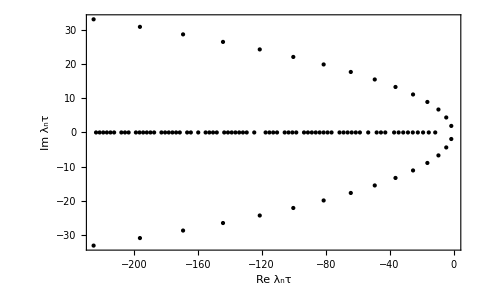

```mathematica
hEV=ListPlot[Table[{Re[λτTest[[n]]],Im[λτTest[[n]]]},{n,Length[λτTest]}],PlotStyle->Directive[Black,PointSize[Medium]],FrameLabel->{"Re λ_nτ","Im λ_nτ"},Frame->True,ImageSize->480]
```

```mathematica
Export["Eigenvalues.pdf",hEV]
```

Eigenvalues.pdf

Checking if the eigenvalues solve the characteristic equation within a reasonable  numerical error (the following should be 0):

```mathematica
Max[Abs[Table[CERS[λτTest[[n]],XrTest,XtTest],{n,Length[λτTest]}]]]
```

6.7449×10^-9

Here we compute the normalized ψ_n(v_res) computed as Eq. (19) cleaning  the spurious complex values which are actually real numbers.

```mathematica
ψH=Table[NResidue[h[λτ,XrTest,XtTest],{λτ,λτTest[[n]]}],{n,Length[λτTest]}];
ψH=Table[If[Abs[Im[ψH[[n]]]]<10^-10,Re[ψH[[n]]],ψH[[n]]],{n,Length[ψH]}]
```

{0.380812-0.37816 ⅈ,0.380812+0.37816 ⅈ,0.38873-0.629643 ⅈ,0.38873+0.629643 ⅈ,0.354485-0.937277 ⅈ,0.354485+0.937277 ⅈ,0.000888788,-0.00101754,0.348486-1.2648 ⅈ,0.348486+1.2648 ⅈ,0.000883576,-0.000353446,0.348066-1.58648 ⅈ,0.348066+1.58648 ⅈ,-0.000551973,0.000833354,0.00014525,-0.000847149,0.348313-1.9062 ⅈ,0.348313+1.9062 ⅈ,-0.000144892,0.000401061,-0.000585181,-0.000720952,0.348613-2.22514 ⅈ,0.348613+2.22514 ⅈ,0.000768557,-0.000275954,-0.000778831,-0.000503174,0.348865-2.5437 ⅈ,0.348865+2.5437 ⅈ,0.000238865,0.000748166,0.000604371,-0.000627149,-0.000738181,0.349064-2.86208 ⅈ,0.349064+2.86208 ⅈ,-0.000307792,0.000331664,0.000732437,0.00064411,0.000149358,-0.000428109,-0.00062025,0.34922-3.18035 ⅈ,0.34922+3.18035 ⅈ,-0.000150756,0.000394343,0.00071998,0.000278248,-0.000241048,-0.000637889,-0.000730876,0.34934-3.49857 ⅈ,0.34934+3.49857 ⅈ,0.00043856,0.000679646,0.000371225,-0.0000821749,-0.000498161,-0.00071772,-0.000662998,-0.000361539,0.349437-3.81674 ⅈ,0.349437+3.81674 ⅈ,0.000470897,0.00070159,0.000686803,0.000439081,-0.000355496,-0.000719805,-0.000572814,0.349514-4.13489 ⅈ,0.349514+4.13489 ⅈ,0.000146416,0.000495268,0.000694642,0.000690477,0.000489273,0.000152457,-0.000535991,-0.000701531,-0.000678979,-0.000477628,0.349578-4.45302 ⅈ,0.349578+4.45302 ⅈ,-0.00015322,0.000208275,0.000688756,0.000691997,0.000526894,-0.000107443,-0.000424149,-0.00064075,-0.000709286,-0.000616452,-0.000385554,0.349629-4.77114 ⅈ,0.349629+4.77114 ⅈ,-0.0000701992,0.00025864,0.000528993,0.000683717,0.000555439,0.000304596,-0.000315372,-0.00055878,-0.000689819}

Normalization factor computed as ratio between normalized and not normalized eigenfunctions ψ:

```mathematica
NFH=Table[ψH[[n]]/ψNN[XrTest,λτTest[[n]]],{n,Length[λτTest]}];
```

Alternative computation relying on the Residue theorem :

```mathematica
NFHres=Table[NResidue[1/(ψNN[XtTest,λτ]-ψNN[XrTest,λτ]),{λτ,λτTest[[n]]}],{n,Length[λτTest]}];
```

and here a comparison between these two sets of normalization factors which are expected to be the same (as they are):

```mathematica
Max[Abs[Table[NFHres[[n]]-NFH[[n]],{n,Length[λτTest]}]]]
```

6.48359×10^-11

#### Fig. 4 of (Vinci & Mattia, 2024): The Fourier transfer function for μ-modulation

```mathematica
TF[s_,Xr_,Xt_]:=ντ/(√σ2τ(1+s))(DxψNN[Xt,s]-DxψNN[Xr,s])/(ψNN[Xt,s]-ψNN[Xr,s]);
```

```mathematica
TF[f_]=TF[ⅈ 2π f τ,XrTest,XtTest];
```

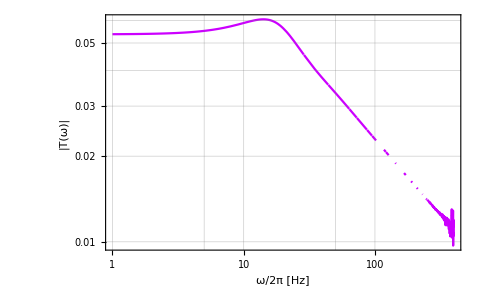

```mathematica
LogLogPlot[Abs[TF[f]],{f,1,400},Frame->True,GridLines->Automatic,FrameLabel->{"ω/2π [Hz]","|T(ω)|"},PlotStyle->Hue[0.8,1,1],ImageSize->480]
```

This is computed with the eigenfunctions ψ expressed in terms of parabolic cylinder functions (more reliable at high Fourier frequencies):

```mathematica
TFD[s_,Xr_,Xt_]:=ντ/(√σ2τ(1+s))(DxψNND[Xt,s]-DxψNND[Xr,s])/(ψNND[Xt,s]-ψNND[Xr,s]);
```

```mathematica
TFD[f_]=TFD[ⅈ 2π f τ,XrTest,XtTest];
```

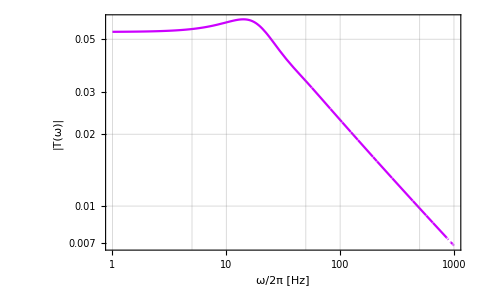

```mathematica
hg=LogLogPlot[Abs[TFD[f]],{f,1,1000},Frame->True,GridLines->Automatic,FrameLabel->{"ω/2π [Hz]","|T(ω)|"},PlotStyle->Hue[0.8,1,1],ImageSize->480]
```

```mathematica
Export["TransferFunctionAbs.pdf",hg]
```

TransferFunctionAbs.pdf

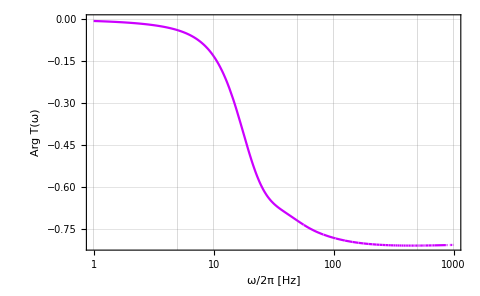

```mathematica
hgArg=LogLinearPlot[Arg[TFD[f]],{f,1,1000},Frame->True,GridLines->Automatic,FrameLabel->{"ω/2π [Hz]","Arg T(ω)"},PlotStyle->Hue[0.8,1,1],ImageSize->480]
```

```mathematica
Export["TransferFunctionArg.pdf",hgArg]
```

TransferFunctionArg.pdf

Here the coefficients  computed from the expression involving the derivatives of the eigenfunctions ψ:

```mathematica
cH=Table[(ντ (DxψNN[XtTest,λτTest[[n]]]-DxψNN[XrTest,λτTest[[n]]])NFH[[n]])/(√σ2τ λτTest[[n]](λτTest[[n]]+1)),{n,Length[λτTest]}]
```

{-0.012614+0.00834478 ⅈ,-0.012614-0.00834478 ⅈ,-0.00385049+0.00030427 ⅈ,-0.00385049-0.00030427 ⅈ,-0.00169405-0.00043785 ⅈ,-0.00169405+0.00043785 ⅈ,-0.00196932,-0.00116917,-0.000772899-0.000454465 ⅈ,-0.000772899+0.000454465 ⅈ,-0.000822828,-0.000629739,-0.000377943-0.000332451 ⅈ,-0.000377943+0.000332451 ⅈ,-0.000506403,-0.000419999,-0.000357266,-0.000309812,-0.000201086-0.00023123 ⅈ,-0.000201086+0.00023123 ⅈ,-0.000272244,-0.000217119,-0.000196659,-0.000179324,-0.000115243-0.00016224 ⅈ,-0.000115243+0.00016224 ⅈ,-0.000151435,-0.000130454,-0.000121821,-0.000114094,-0.0000702494-0.000116473 ⅈ,-0.0000702494+0.000116473 ⅈ,-0.000107132,-0.000100863,-0.0000952277,-0.0000855341,-0.0000813031,-0.000045054-0.0000857392 ⅈ,-0.000045054+0.0000857392 ⅈ,-0.0000773972,-0.0000737853,-0.0000704518,-0.0000673813,-0.0000645504,-0.0000619284,-0.0000571909,-0.0000301368-0.0000646277 ⅈ,-0.0000301368+0.0000646277 ⅈ,-0.0000550337,-0.0000530047,-0.0000511004,-0.000047646,-0.0000460765,-0.0000445953,-0.0000431905,-0.0000208808-0.0000497659 ⅈ,-0.0000208808+0.0000497659 ⅈ,-0.0000393677,-0.000037125,-0.0000360906,-0.0000351086,-0.0000341734,-0.0000332791,-0.0000324211,-0.0000315965,-0.0000149051-0.0000390545 ⅈ,-0.0000149051+0.0000390545 ⅈ,-0.000030043,-0.0000293141,-0.0000286168,-0.0000279502,-0.0000267001,-0.0000255429,-0.0000249932,-0.0000109138-0.0000311658 ⅈ,-0.0000109138+0.0000311658 ⅈ,-0.0000239465,-0.0000234493,-0.0000229697,-0.0000225078,-0.0000220632,-0.0000216349,-0.0000208223,-0.000020435,-0.0000200587,-0.0000196927,-8.169×10^-6-0.000025241 ⅈ,-8.169×10^-6+0.000025241 ⅈ,-0.0000193366,-0.0000189903,-0.0000183282,-0.0000180126,-0.0000177072,-0.0000171251,-0.0000168469,-0.0000165762,-0.0000163123,-0.0000160547,-0.000015803,-6.23283×10^-6-0.0000207125 ⅈ,-6.23283×10^-6+0.0000207125 ⅈ}

These are the same coefficients directly computed from the residue of the transfer function:

```mathematica
cHres=Table[NResidue[TFD[λτ,XrTest,XtTest],{λτ,λτTest[[n]]}]/λτTest[[n]],{n,Length[λτTest]}]
```

{-0.012614+0.00834478 ⅈ,-0.012614-0.00834478 ⅈ,-0.00385049+0.00030427 ⅈ,-0.00385049-0.00030427 ⅈ,-0.00169405-0.00043785 ⅈ,-0.00169405+0.00043785 ⅈ,-0.00196932,-0.00116917,-0.000772899-0.000454465 ⅈ,-0.000772899+0.000454465 ⅈ,-0.000822828,-0.000629739,-0.000377943-0.000332451 ⅈ,-0.000377943+0.000332451 ⅈ,-0.000506403,-0.000419999,-0.000357266,-0.000309812,-0.000201086-0.00023123 ⅈ,-0.000201086+0.00023123 ⅈ,-0.000272244,-0.000217119,-0.000196659,-0.000179324,-0.000115243-0.00016224 ⅈ,-0.000115243+0.00016224 ⅈ,-0.000151435,-0.000130454,-0.000121821,-0.000114094,-0.0000702494-0.000116473 ⅈ,-0.0000702494+0.000116473 ⅈ,-0.000107132,-0.000100863,-0.0000952277,-0.0000855341,-0.0000813031,-0.000045054-0.0000857392 ⅈ,-0.000045054+0.0000857392 ⅈ,-0.0000773972,-0.0000737853,-0.0000704518,-0.0000673813,-0.0000645504,-0.0000619284,-0.0000571909,-0.0000301368-0.0000646277 ⅈ,-0.0000301368+0.0000646277 ⅈ,-0.0000550337,-0.0000530047,-0.0000511004,-0.000047646,-0.0000460765,-0.0000445953,-0.0000431905,-0.0000208808-0.0000497659 ⅈ,-0.0000208808+0.0000497659 ⅈ,-0.0000393677,-0.000037125,-0.0000360906,-0.0000351086,-0.0000341734,-0.0000332791,-0.0000324211,-0.0000315965,-0.000014905-0.0000390545 ⅈ,-0.000014905+0.0000390545 ⅈ,-0.000030043,-0.0000293141,-0.0000286168,-0.0000279502,-0.0000267001,-0.0000255429,-0.0000249932,-0.0000109138-0.0000311658 ⅈ,-0.0000109138+0.0000311658 ⅈ,-0.0000239465,-0.0000234493,-0.0000229697,-0.0000225078,-0.0000220632,-0.0000216349,-0.0000208223,-0.000020435,-0.0000200587,-0.0000196927,-8.16902×10^-6-0.000025241 ⅈ,-8.16902×10^-6+0.000025241 ⅈ,-0.0000193366,-0.0000189903,-0.0000183282,-0.0000180126,-0.0000177072,-0.0000171251,-0.0000168469,-0.0000165762,-0.0000163123,-0.0000160547,-0.000015803,-6.23282×10^-6-0.0000207125 ⅈ,-6.23282×10^-6+0.0000207125 ⅈ}

And this two way to compute the coupling coefficient lead to the same result:

```mathematica
Max[Abs[Table[cHres[[n]]-cH[[n]],{n,Length[λτTest]}]]]
```

6.05789×10^-11

```mathematica
cH[[1]]
```

-0.012614+0.00834478 ⅈ

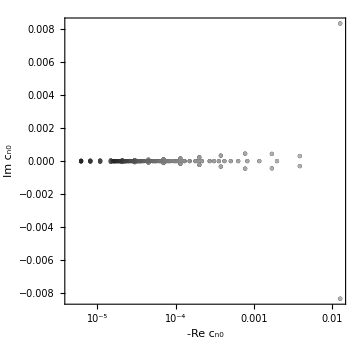

```mathematica
hCn0=ListLogLinearPlot[Table[Style[{-Re[cH[[n]]],Im[cH[[n]]]},GrayLevel[(125-n)/175]],{n,Length[λτTest]}],FrameLabel->{"-Re c_n0","Im c_n0"},Frame->True,ImageSize->360,PlotStyle->Directive[Black,PointSize[Large]],PlotRange->All,AspectRatio->1]
```

```mathematica
Export["Cn0distribution.pdf",hCn0]
```

Cn0distribution.pdf

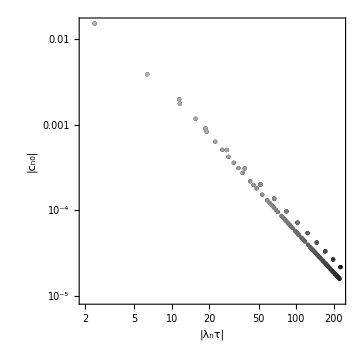

```mathematica
hCn0vsλτn=ListLogLogPlot[Table[Style[{Abs[λτTest[[n]]],Abs[cH[[n]]]},GrayLevel[(125-n)/175]],{n,Length[λτTest]}],FrameLabel->{"|λ_nτ|","|c_n0|"},Frame->True,ImageSize->360,PlotStyle->Directive[Black,PointSize[Large]],PlotRange->All,AspectRatio->1]
```

```mathematica
Export["AbsCn0VsAbsLambdanTau.pdf",hCn0vsλτn]
```

AbsCn0VsAbsLambdanTau.pdf

Here to show that |c_n0| = β n^-α, with both α and β positive real constants:

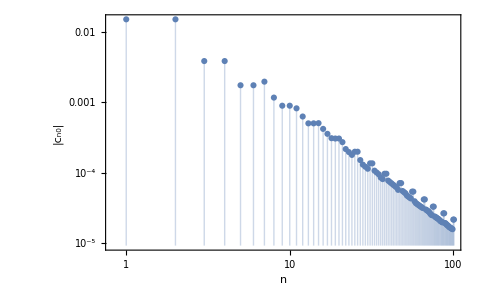

```mathematica
ListLogLogPlot[Abs[cH],Filling->Axis,Frame->True,PlotRange->All,FrameLabel->{"n","|c_n0|"},ImageSize->480]
```

The following plot is to say that also the module of the eigenvalues grows as a power law as well, meaning that  |c_n0| are proportional to |λ_n τ|^-γ with γ a positive real constant:

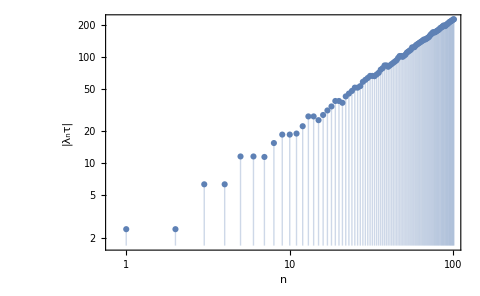

```mathematica
ListLogLogPlot[Abs[λτTest],Filling->Axis,Frame->True,PlotRange->All,FrameLabel->{"n","|λ_nτ|"},ImageSize->480]
```

```mathematica
DΦDμ=-(Derivative[1,0][Φ][XrTest,XtTest]+Derivative[0,1][Φ][XrTest,XtTest])/(√σ2τ);
TFse[s_,NoM_]:=DΦDμ+s∑_(n=1)^NoM cH[[n]]/(s-λτTest[[n]]);
DΦDμ
```

NIntegrate::inumr: The integrand -2 ⅇ^(-w^2+2 w System`Private`DerivativeX[1]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

0.0536303

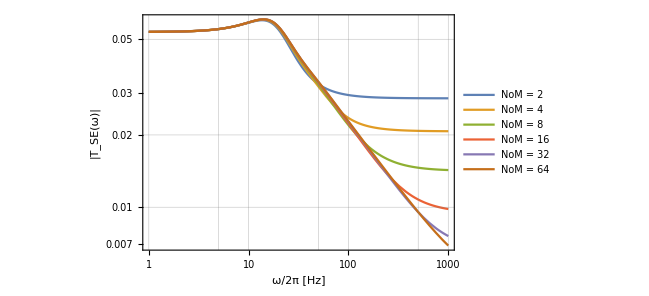

```mathematica
hgSE=LogLogPlot[{Abs[TFse[ⅈ 2π f τ,2]],Abs[TFse[ⅈ 2π f τ,4]],Abs[TFse[ⅈ 2π f τ,8]],Abs[TFse[ⅈ 2π f τ,16]],Abs[TFse[ⅈ 2π f τ,32]],Abs[TFse[ⅈ 2π f τ,64]]},{f,1,1000},Frame->True,GridLines->Automatic,PlotLegends->{"NoM = 2","NoM = 4","NoM = 8","NoM = 16","NoM = 32","NoM = 64"},FrameLabel->{"ω/2π [Hz]","|T_SE(ω)|"},ImageSize->480]
```

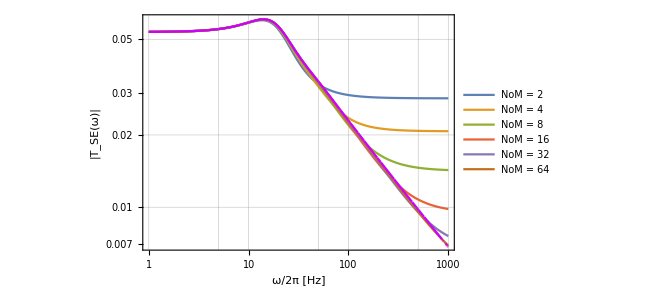

```mathematica
hTF=Show[hgSE,hg,ImageSize->480]
```

```mathematica
Export["TransferFunctionSE.pdf",hTF]
```

TransferFunctionSE.pdf

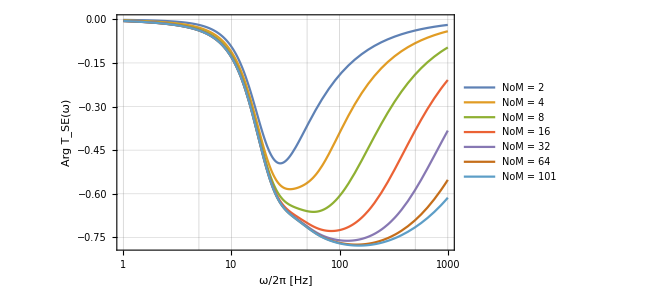

```mathematica
hgArgSE=LogLinearPlot[{Arg[TFse[ⅈ 2π f τ,2]],Arg[TFse[ⅈ 2π f τ,4]],Arg[TFse[ⅈ 2π f τ,8]],Arg[TFse[ⅈ 2π f τ,16]],Arg[TFse[ⅈ 2π f τ,32]],Arg[TFse[ⅈ 2π f τ,64]],Arg[TFse[ⅈ 2π f τ,101]]},{f,1,1000},Frame->True,GridLines->Automatic,PlotLegends->{"NoM = 2","NoM = 4","NoM = 8","NoM = 16","NoM = 32","NoM = 64","NoM = 101"},FrameLabel->{"ω/2π [Hz]","Arg T_SE(ω)"},ImageSize->480]
```

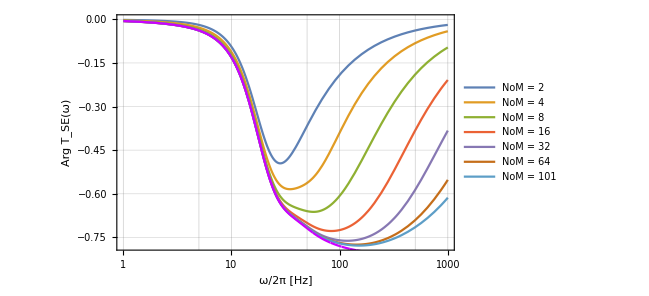

```mathematica
hArgTF=Show[hgArgSE,hgArg,ImageSize->480]
```

```mathematica
Export["TransferFunctionSEArg.pdf",hArgTF]
```

TransferFunctionSEArg.pdf

#### Fig. 5 of (Vinci & Mattia, 2024): The Fourier transfer function for σ-modulation:

```mathematica
TFσ[s_,Xr_,Xt_]:=ντ/(σ2τ(2+s))(s+(Xt DxψNN[Xt,s]-Xr DxψNN[Xr,s])/(ψNN[Xt,s]-ψNN[Xr,s]));
```

```mathematica
TFσ[f_]=TFσ[ⅈ 2π f τ,XrTest,XtTest];
```

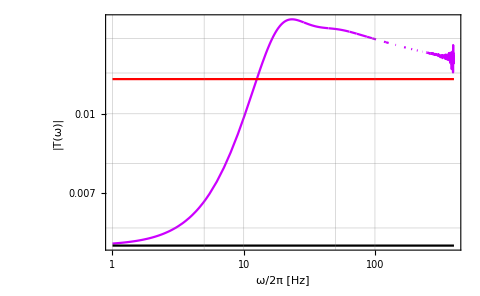

```mathematica
LogLogPlot[{Abs[TFσ[f]],ντ/σ2τ,DΦDσ2},{f,1,400},Frame->True,GridLines->Automatic,FrameLabel->{"ω/2π [Hz]","|T(ω)|"},PlotStyle->{Hue[0.8,1,1],Red,Black},ImageSize->480]
```

This is computed with the eigenfunctions ψ expressed in terms of parabolic cylinder functions (more reliable at high Fourier frequencies):

```mathematica
TFDσ[s_,Xr_,Xt_]:=ντ/(σ2τ(2+s))(s+(Xt DxψNND[Xt,s]-Xr DxψNND[Xr,s])/(ψNND[Xt,s]-ψNND[Xr,s]));
```

```mathematica
TFDσ[f_]=TFDσ[ⅈ 2π f τ,XrTest,XtTest];
```

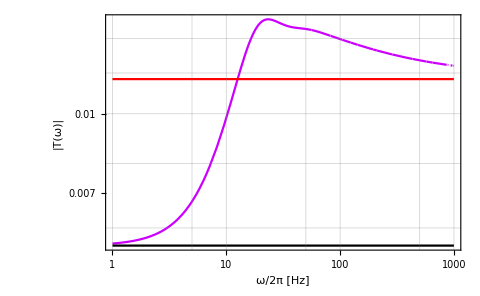

```mathematica
hgσ=LogLogPlot[{Abs[TFDσ[f]],ντ/σ2τ,DΦDσ2},{f,1,1000},Frame->True,GridLines->Automatic,FrameLabel->{"ω/2π [Hz]","|T(ω)|"},PlotStyle->{Hue[0.8,1,1],Red,Black},ImageSize->480]
```

```mathematica
Export["TransferFunctionSigmaAbs.pdf",hgσ]
```

TransferFunctionSigmaAbs.pdf

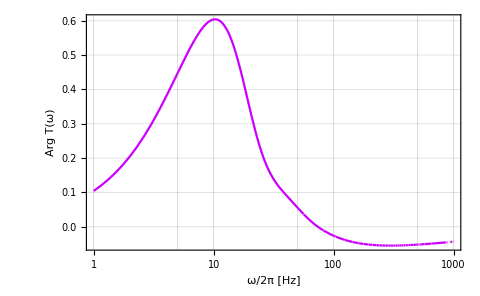

```mathematica
hgArgσ=LogLinearPlot[Arg[TFDσ[f]],{f,1,1000},Frame->True,GridLines->Automatic,FrameLabel->{"ω/2π [Hz]","Arg T(ω)"},PlotStyle->Hue[0.8,1,1],ImageSize->480]
```

```mathematica
Export["TransferFunctionSigmaArg.pdf",hgArgσ]
```

TransferFunctionSigmaArg.pdf

Here the coefficients  computed from the expression involving the derivatives of the eigenfunctions ψ:

```mathematica
cHσ=Table[-((ντ (XtTest DxψNN[XtTest,λτTest[[n]]]-XrTest DxψNN[XrTest,λτTest[[n]]])NFH[[n]])/(2σ2τ λτTest[[n]](λτTest[[n]]+2))),{n,Length[λτTest]}]
```

{-0.00106475-0.00199997 ⅈ,-0.00106475+0.00199997 ⅈ,7.70809×10^-6-0.00112054 ⅈ,7.70809×10^-6+0.00112054 ⅈ,0.000191949-0.000752595 ⅈ,0.000191949+0.000752595 ⅈ,-0.000914728,-0.000526862,0.000273913-0.000477646 ⅈ,0.000273913+0.000477646 ⅈ,-0.00036584,-0.000276962,0.00025615-0.000295609 ⅈ,0.00025615+0.000295609 ⅈ,-0.000221806,-0.000183029,-0.000154859,-0.000134027,0.000215752-0.000189474 ⅈ,0.000215752+0.000189474 ⅈ,-0.000117662,-0.0000932781,-0.0000843713,-0.0000769412,0.000177351-0.000126847 ⅈ,0.000177351+0.000126847 ⅈ,-0.0000648288,-0.0000556611,-0.0000519853,-0.0000487095,0.000145822-0.0000884021 ⅈ,0.000145822+0.0000884021 ⅈ,-0.0000457217,-0.0000429883,-0.0000405202,-0.000036359,-0.0000345806,0.000120907-0.0000637858 ⅈ,0.000120907+0.0000637858 ⅈ,-0.0000329325,-0.000031385,-0.0000299349,-0.0000285932,-0.0000273675,-0.0000262519,-0.0000242702,0.000101335-0.0000474034 ⅈ,0.000101335+0.0000474034 ⅈ,-0.0000233613,-0.000022492,-0.0000216646,-0.0000201622,-0.000019493,-0.0000188721,-0.0000182888,0.0000858751-0.0000361246 ⅈ,0.0000858751+0.0000361246 ⅈ,-0.0000166758,-0.0000156993,-0.0000152507,-0.000014831,-0.0000144381,-0.0000140673,-0.0000137129,-0.0000133699,0.000073541-0.000028127 ⅈ,0.000073541+0.000028127 ⅈ,-0.0000127088,-0.000012392,-0.0000120875,-0.000011798,-0.0000112667,-0.0000107884,-0.000010562,0.0000635904-0.000022309 ⅈ,0.0000635904+0.000022309 ⅈ,-0.0000101228,-9.90906×10^-6,-9.70043×10^-6,-9.49861×10^-6,-9.3052×10^-6,-9.12113×10^-6,-8.78025×10^-6,-8.62102×10^-6,-8.46689×10^-6,-8.31618×10^-6,0.0000554719-0.0000179809 ⅈ,0.0000554719+0.0000179809 ⅈ,-8.16768×10^-6,-8.02092×10^-6,-7.73421×10^-6,-7.59617×10^-6,-7.46308×10^-6,-7.21404×10^-6,-7.09793×10^-6,-6.98652×10^-6,-6.87874×10^-6,-6.77347×10^-6,-6.66975×10^-6,0.0000487766-0.0000146977 ⅈ,0.0000487766+0.0000146977 ⅈ,-6.567×10^-6,-6.46503×10^-6,-6.36411×10^-6,-6.2648×10^-6,-6.07385×10^-6,-5.98342×10^-6,-5.81368×10^-6,-5.73386×10^-6,-5.65666×10^-6}

New formula

```mathematica
cHσ=Table[((ντ (XtTest DxψNN[XtTest,λτTest[[n]]]-XrTest DxψNN[XrTest,λτTest[[n]]])NFH[[n]])/(σ2τ λτTest[[n]](λτTest[[n]]+2))),{n,Length[λτTest]}]
```

{0.00212949+0.00399995 ⅈ,0.00212949-0.00399995 ⅈ,-0.0000154162+0.00224108 ⅈ,-0.0000154162-0.00224108 ⅈ,-0.000383898+0.00150519 ⅈ,-0.000383898-0.00150519 ⅈ,0.00182946,0.00105372,-0.000547826+0.000955292 ⅈ,-0.000547826-0.000955292 ⅈ,0.000731679,0.000553925,-0.0005123+0.000591218 ⅈ,-0.0005123-0.000591218 ⅈ,0.000443613,0.000366059,0.000309719,0.000268054,-0.000431505+0.000378947 ⅈ,-0.000431505-0.000378947 ⅈ,0.000235324,0.000186556,0.000168743,0.000153882,-0.000354701+0.000253694 ⅈ,-0.000354701-0.000253694 ⅈ,0.000129658,0.000111322,0.000103971,0.000097419,-0.000291643+0.000176804 ⅈ,-0.000291643-0.000176804 ⅈ,0.0000914433,0.0000859766,0.0000810405,0.000072718,0.0000691613,-0.000241813+0.000127572 ⅈ,-0.000241813-0.000127572 ⅈ,0.0000658651,0.0000627699,0.0000598698,0.0000571864,0.0000547351,0.0000525038,0.0000485405,-0.000202671+0.0000948069 ⅈ,-0.000202671-0.0000948069 ⅈ,0.0000467225,0.0000449841,0.0000433291,0.0000403244,0.0000389861,0.0000377442,0.0000365776,-0.00017175+0.0000722493 ⅈ,-0.00017175-0.0000722493 ⅈ,0.0000333516,0.0000313986,0.0000305014,0.0000296619,0.0000288761,0.0000281346,0.0000274258,0.0000267398,-0.000147082+0.0000562541 ⅈ,-0.000147082-0.0000562541 ⅈ,0.0000254176,0.0000247839,0.0000241751,0.000023596,0.0000225333,0.0000215768,0.0000211239,-0.000127181+0.000044618 ⅈ,-0.000127181-0.000044618 ⅈ,0.0000202456,0.0000198181,0.0000194009,0.0000189972,0.0000186104,0.0000182423,0.0000175605,0.000017242,0.0000169338,0.0000166324,-0.000110944+0.0000359619 ⅈ,-0.000110944-0.0000359619 ⅈ,0.0000163354,0.0000160418,0.0000154684,0.0000151923,0.0000149262,0.0000144281,0.0000141959,0.000013973,0.0000137575,0.0000135469,0.0000133395,-0.0000975531+0.0000293954 ⅈ,-0.0000975531-0.0000293954 ⅈ,0.000013134,0.0000129301,0.0000127282,0.0000125296,0.0000121477,0.0000119668,0.0000116274,0.0000114677,0.0000113133}

These are the same coefficients directly computed from the residue of the transfer function:

```mathematica
cHσres=Table[NResidue[TFDσ[λτ,XrTest,XtTest],{λτ,λτTest[[n]]}]/λτTest[[n]],{n,Length[λτTest]}]
```

{0.00212949+0.00399995 ⅈ,0.00212949-0.00399995 ⅈ,-0.0000154162+0.00224108 ⅈ,-0.0000154162-0.00224108 ⅈ,-0.000383898+0.00150519 ⅈ,-0.000383898-0.00150519 ⅈ,0.00182946-1.65398×10^-19 ⅈ,0.00105372-7.5083×10^-20 ⅈ,-0.000547826+0.000955292 ⅈ,-0.000547826-0.000955292 ⅈ,0.000731679-6.63131×10^-20 ⅈ,0.000553925-4.6064×10^-20 ⅈ,-0.0005123+0.000591218 ⅈ,-0.0005123-0.000591218 ⅈ,0.000443613-2.79724×10^-20 ⅈ,0.000366059-4.35846×10^-20 ⅈ,0.000309719-2.07814×10^-20 ⅈ,0.000268054-1.78175×10^-20 ⅈ,-0.000431505+0.000378947 ⅈ,-0.000431505-0.000378947 ⅈ,0.000235324-1.66374×10^-20 ⅈ,0.000186556-2.978×10^-20 ⅈ,0.000168743-4.36683×10^-21 ⅈ,0.000153882-7.03695×10^-21 ⅈ,-0.000354701+0.000253694 ⅈ,-0.000354701-0.000253694 ⅈ,0.000129658-6.42094×10^-21 ⅈ,0.000111322-7.65415×10^-21 ⅈ,0.000103971-1.12801×10^-21 ⅈ,0.000097419-6.56399×10^-21 ⅈ,-0.000291643+0.000176804 ⅈ,-0.000291643-0.000176804 ⅈ,0.0000914433-3.93683×10^-21 ⅈ,0.0000859766+9.40167×10^-22 ⅈ,0.0000810405-8.16279×10^-21 ⅈ,0.000072718+1.92112×10^-21 ⅈ,0.0000691613-1.36804×10^-22 ⅈ,-0.000241813+0.000127572 ⅈ,-0.000241813-0.000127572 ⅈ,0.0000658651-1.17782×10^-20 ⅈ,0.0000627699-2.03393×10^-21 ⅈ,0.0000598698-9.97971×10^-21 ⅈ,0.0000571864-1.68786×10^-20 ⅈ,0.0000547351-6.43794×10^-21 ⅈ,0.0000525038+4.65669×10^-21 ⅈ,0.0000485405-7.91196×10^-21 ⅈ,-0.000202671+0.0000948069 ⅈ,-0.000202671-0.0000948069 ⅈ,0.0000467225-7.05924×10^-22 ⅈ,0.0000449841-2.19369×10^-21 ⅈ,0.0000433291-4.0017×10^-21 ⅈ,0.0000403244-1.42578×10^-21 ⅈ,0.0000389861+3.44124×10^-22 ⅈ,0.0000377442-1.62887×10^-21 ⅈ,0.0000365776+1.11899×10^-21 ⅈ,-0.00017175+0.0000722493 ⅈ,-0.00017175-0.0000722493 ⅈ,0.0000333516-7.73234×10^-21 ⅈ,0.0000313986-8.66722×10^-22 ⅈ,0.0000305014-1.88257×10^-21 ⅈ,0.0000296619-2.55727×10^-21 ⅈ,0.0000288761-1.45425×10^-21 ⅈ,0.0000281346+1.80269×10^-21 ⅈ,0.0000274258-2.58281×10^-21 ⅈ,0.0000267398-9.32116×10^-22 ⅈ,-0.000147082+0.000056254 ⅈ,-0.000147082-0.000056254 ⅈ,0.0000254176-2.48994×10^-21 ⅈ,0.0000247839-5.61968×10^-21 ⅈ,0.0000241751-8.54137×10^-21 ⅈ,0.000023596-3.01778×10^-21 ⅈ,0.0000225333-7.02189×10^-22 ⅈ,0.0000215768+5.38083×10^-21 ⅈ,0.0000211239-3.15793×10^-21 ⅈ,-0.000127181+0.0000446179 ⅈ,-0.000127181-0.0000446179 ⅈ,0.0000202456-2.43068×10^-21 ⅈ,0.0000198181-4.94607×10^-21 ⅈ,0.0000194009-7.9845×10^-21 ⅈ,0.0000189972+1.08963×10^-22 ⅈ,0.0000186104-1.47024×10^-21 ⅈ,0.0000182423-1.44001×10^-21 ⅈ,0.0000175605-2.01515×10^-21 ⅈ,0.000017242-6.71207×10^-22 ⅈ,0.0000169338+7.3067×10^-22 ⅈ,0.0000166324+4.5547×10^-22 ⅈ,-0.000110944+0.0000359619 ⅈ,-0.000110944-0.0000359619 ⅈ,0.0000163354-8.45471×10^-22 ⅈ,0.0000160418-1.00945×10^-21 ⅈ,0.0000154684-4.02173×10^-21 ⅈ,0.0000151923-1.88895×10^-22 ⅈ,0.0000149262+2.59489×10^-22 ⅈ,0.0000144281+4.97739×10^-22 ⅈ,0.0000141959+1.51766×10^-21 ⅈ,0.000013973+3.18268×10^-21 ⅈ,0.0000137575-1.63397×10^-21 ⅈ,0.0000135469-7.5019×10^-22 ⅈ,0.0000133395+3.37552×10^-22 ⅈ,-0.0000975531+0.0000293954 ⅈ,-0.0000975531-0.0000293954 ⅈ,0.000013134-5.72878×10^-23 ⅈ,0.0000129301-3.32765×10^-21 ⅈ,0.0000127282-5.89747×10^-22 ⅈ,0.0000125296-1.50181×10^-21 ⅈ,0.0000121477-3.85605×10^-21 ⅈ,0.0000119668-2.92794×10^-21 ⅈ,0.0000116274-5.30587×10^-22 ⅈ,0.0000114677+7.18523×10^-22 ⅈ,0.0000113133+2.78735×10^-21 ⅈ}

And this two way to compute the coupling coefficient lead to the same result:

```mathematica
Max[Abs[Table[cHσres[[n]]-cHσ[[n]],{n,Length[λτTest]}]]]
```

1.08991×10^-10

```mathematica
cHσ[[1]]
```

0.00212949+0.00399995 ⅈ

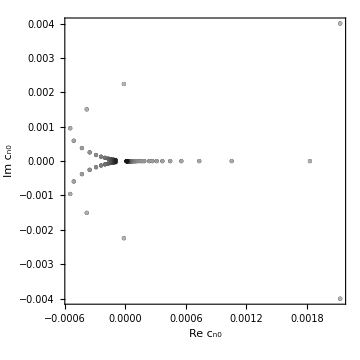

```mathematica
hCn0σ=ListPlot[Table[Style[{Re[cHσ[[n]]],Im[cHσ[[n]]]},GrayLevel[(125-n)/175]],{n,Length[λτTest]}],FrameLabel->{"Re c_n0","Im c_n0"},Frame->True,ImageSize->360,PlotStyle->Directive[Black,PointSize[Large]],PlotRange->All,AspectRatio->1]
```

```mathematica
Export["Cn0SigmaDistribution.pdf",hCn0σ]
```

Cn0SigmaDistribution.pdf

```mathematica
Take[λτTest,8]
```

{-1.44824-1.91068 ⅈ,-1.44824+1.91068 ⅈ,-4.59833-4.37306 ⅈ,-4.59833+4.37306 ⅈ,-9.4864-6.70067 ⅈ,-9.4864+6.70067 ⅈ,-11.4891,-15.5349}

```mathematica
Take[cHσ,8]
```

{0.00212949+0.00399995 ⅈ,0.00212949-0.00399995 ⅈ,-0.0000154162+0.00224108 ⅈ,-0.0000154162-0.00224108 ⅈ,-0.000383898+0.00150519 ⅈ,-0.000383898-0.00150519 ⅈ,0.00182946,0.00105372}

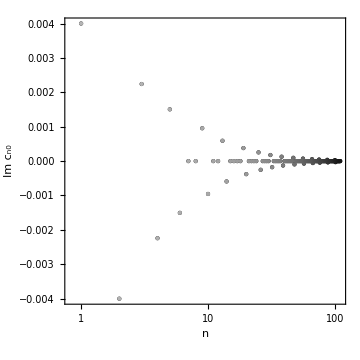

```mathematica
ListLogLinearPlot[Table[Style[{n,Im[cHσ[[n]]]},GrayLevel[(125-n)/175]],{n,Length[λτTest]}],FrameLabel->{"n","Im c_n0"},Frame->True,ImageSize->360,PlotStyle->Directive[Black,PointSize[Large]],PlotRange->All,AspectRatio->1]
```

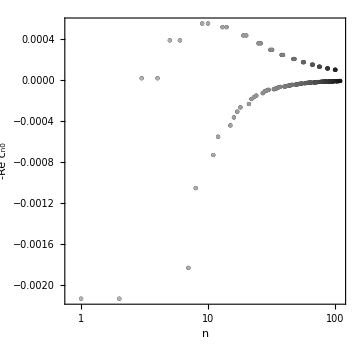

```mathematica
ListLogLinearPlot[Table[Style[{n,-Re[cHσ[[n]]]},GrayLevel[(125-n)/175]],{n,Length[λτTest]}],FrameLabel->{"n","-Re c_n0"},Frame->True,ImageSize->360,PlotStyle->Directive[Black,PointSize[Large]],PlotRange->All,AspectRatio->1]
```

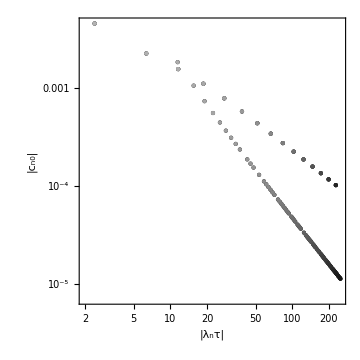

```mathematica
hCn0σvsλτn=ListLogLogPlot[Table[Style[{Abs[λτTest[[n]]],Abs[cHσ[[n]]]},GrayLevel[(125-n)/175]],{n,Length[λτTest]}],FrameLabel->{"|λ_nτ|","|c_n0|"},Frame->True,ImageSize->360,PlotStyle->Directive[Black,PointSize[Large]],PlotRange->All,AspectRatio->1]
```

```mathematica
Export["AbsCn0SigmaVsAbsLambdanTau.pdf",hCn0σvsλτn]
```

AbsCn0SigmaVsAbsLambdanTau.pdf

In what follows for some reasons (I have no time to understand why) the derivative DΦDσ2 does not match with TFDσ[0]

```mathematica
DΦDσ2=-1/(2σ2τ)(XrTest Derivative[1,0][Φ][XrTest,XtTest]+XtTest Derivative[0,1][Φ][XrTest,XtTest]);
(*DΦDσ2=Re[TFDσ[0.001]]*)
TFseσ[s_,NoM_]:=DΦDσ2+s∑_(n=1)^NoM cHσ[[n]]/(s-λτTest[[n]]);
DΦDσ2
```

0.00554493

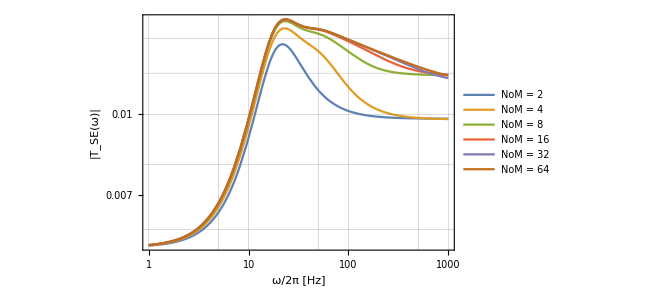

```mathematica
hgσSE=LogLogPlot[{Abs[TFseσ[ⅈ 2π f τ,2]],Abs[TFseσ[ⅈ 2π f τ,4]],Abs[TFseσ[ⅈ 2π f τ,8]],Abs[TFseσ[ⅈ 2π f τ,16]],Abs[TFseσ[ⅈ 2π f τ,32]],Abs[TFseσ[ⅈ 2π f τ,64]]},{f,1,1000},Frame->True,GridLines->Automatic,PlotLegends->{"NoM = 2","NoM = 4","NoM = 8","NoM = 16","NoM = 32","NoM = 64"},FrameLabel->{"ω/2π [Hz]","|T_SE(ω)|"},ImageSize->480]
```

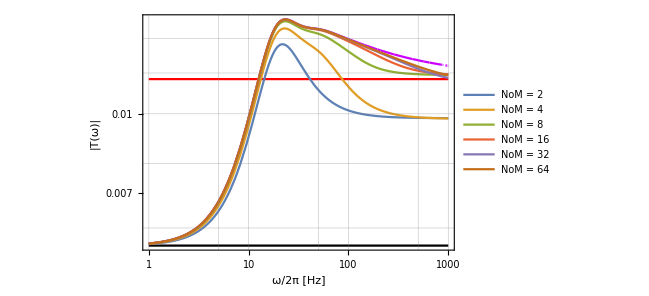

```mathematica
hTFσ=Show[hgσ,hgσSE,ImageSize->480,PlotRange->All]
```

```mathematica
Export["TransferFunctionSigmaSE.pdf",hTFσ]
```

TransferFunctionSigmaSE.pdf

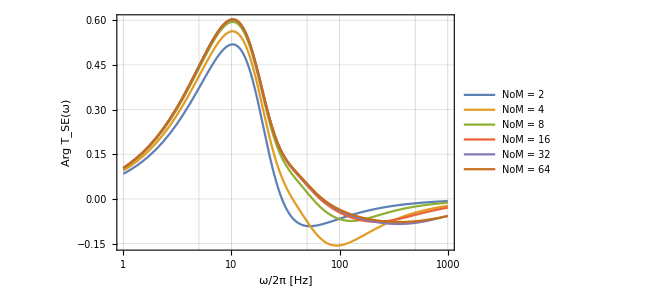

```mathematica
hgArgSEσ=LogLinearPlot[{Arg[TFseσ[ⅈ 2π f τ,2]],Arg[TFseσ[ⅈ 2π f τ,4]],Arg[TFseσ[ⅈ 2π f τ,8]],Arg[TFseσ[ⅈ 2π f τ,16]],Arg[TFseσ[ⅈ 2π f τ,32]],Arg[TFseσ[ⅈ 2π f τ,64]]},{f,1,1000},Frame->True,GridLines->Automatic,PlotLegends->{"NoM = 2","NoM = 4","NoM = 8","NoM = 16","NoM = 32","NoM = 64"},FrameLabel->{"ω/2π [Hz]","Arg T_SE(ω)"},ImageSize->480]
```

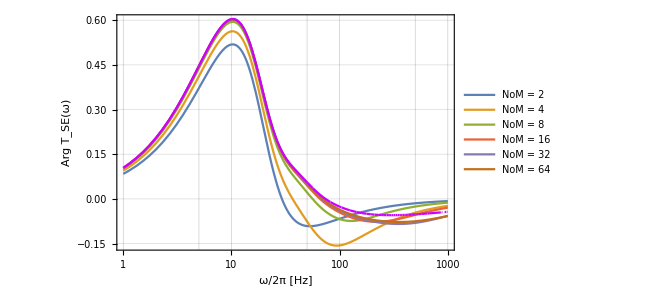

```mathematica
hArgTFσ=Show[hgArgSEσ,hgArgσ,ImageSize->480]
```

```mathematica
Export["TransferFunctionSEArgSigma.pdf",hArgTFσ]
```

TransferFunctionSEArgSigma.pdf